```mathematica
(*Question 1*)
P[n_,r_,t_]:=((r*t)^n*Exp[-r*t])/(n!)
```

```mathematica
FullSimplify[Sum[((r*t)^n*Exp[-r*t])/(n!),{n,nc,∞}]]
FullSimplify[Sum[((r*t)^n*Exp[-r*t])/(n!),{n,0,nc}]]
FullSimplify[Sum[((r*t)^n*Exp[-r*t])/(n!),{n,0,∞}]]
```

1-Gamma[nc,r t]/Gamma[nc]

Gamma[1+nc,r t]/Gamma[1+nc]

1

```mathematica
FullSimplify[a^2*Sum[P[n,rb,t],{n,nc,∞}]]
FullSimplify[b^2*Sum[P[n,rb+r1,t],{n,0,nc-1}]]
Perr[a_,b_,rb_,r1_,t_,nc_]:=Assuming[Element[n,Integers],FullSimplify[a^2*Sum[P[n,rb,t],{n,nc,∞}]+b^2*Sum[P[n,rb+r1,t],{n,0,nc-1}]]]
Perr[a,b,rb,r1,t,nc]
```

a^2 (1-Gamma[nc,rb t]/Gamma[nc])

(b^2 Gamma[nc,(r1+rb) t])/Gamma[nc]

(a^2 (Gamma[nc]-Gamma[nc,rb t])+b^2 Gamma[nc,(r1+rb) t])/Gamma[nc]

```mathematica
(*1b*)
FullSimplify[Perr[1/(√2),1/(√2),200,5000,0.001,nc]]
```

(0.5 Gamma[nc]-0.5 Gamma[nc,0.2]+0.5 Gamma[nc,5.2])/Gamma[nc]

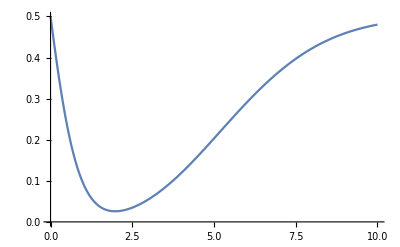

{0.0258424,{nc→1.97724}}

```mathematica
Plot[(0.5 Gamma[nc]-0.5 Gamma[nc,0.2]+0.5 Gamma[nc,5.2])/Gamma[nc],{nc,0,10}]
Minimize[{(0.5 Gamma[nc]-0.5 Gamma[nc,0.2]+0.5 Gamma[nc,5.2])/Gamma[nc],nc≥0},nc]
```

```mathematica
Perr[1/(√2),1/(√2),200,500,0.001,1.9772361351593732]
```

0.257578

```mathematica
Minimize[{FullSimplify[Perr[1/(√2),1/(√2),200,5000,0.001,nc]],nc≥0},nc]
%[1]
Perr[1/(√2),1/(√2),200,5000,0.001,nc]
```

{0.0258424,{nc→1.97724}}

{0.0258424,{nc→1.97724}}[1]

```mathematica
1/Gamma[2](0.5 Gamma[2]-0.5 Gamma[2,0.2]+0.5 Gamma[2,5.2])
```

0.0258629

```mathematica
(*1c*)
Perr[1,0,200,5000,0.001,2]
Perr[0,1,200,5000,0.001,2]
Perr[1/(√2),1/(√2),200,5000,0.001,2]
```

0.0175231

0.0342027

0.0258629

```mathematica
(*1d*)
p1=DiscretePlot3D[10^-4,{nc,0,10},{t,0.001,0.01,0.001},PlotStyle->Orange];
p2=DiscretePlot3D[Perr[1/(√2),1/(√2),200,5000,t,nc],{nc,0,10},{t,0.001,0.01,0.001}];
Show[p1,p2]
```

```mathematica
(*Question 2*)
```

```mathematica
tpulse=(π/2)/omegasbprime;
omegasb=eta^2*omega1^2/(2*delta);
omegac=omega1^2/(2*delta);
omegasbprime=(omegasb^2+delta^2)^(1/2);
omegacprime=(omegac^2+delta^2)^(1/2);
P1=FullSimplify[1/τ Integrate[omegasb^2/omegasbprime^2*Sin[(omegasbprime*t)/2]^2,{t,0,tpulse}]]
tpulse=π/omegacprime;
P2=FullSimplify[1/τ Integrate[omegac^2/omegacprime^2*Sin[(omegacprime*t)/2]^2,{t,0,tpulse}]]
tpulse=π/omegasbprime;
P3=FullSimplify[1/τ Integrate[omegasb^2/omegasbprime^2*Sin[(omegasbprime*t)/2]^2,{t,0,tpulse}]]
```

(eta^4 omega1^4 (-2+π))/(2 (4 delta^4+eta^4 omega1^4) √(4 delta^2+(eta^4 omega1^4)/delta^2) τ)

(omega1^4 π)/(delta^2 ((4 delta^4+omega1^4)/delta^2)^(3/2) τ)

(eta^4 omega1^4 π)/((4 delta^4+eta^4 omega1^4) √(4 delta^2+(eta^4 omega1^4)/delta^2) τ)

```mathematica
Ptot=FullSimplify[P1+P2+P3]
```

1/(2 τ)omega1^4 ((eta^4 (-2+π))/((4 delta^4+eta^4 omega1^4) √(4 delta^2+(eta^4 omega1^4)/delta^2))+(2 π)/(delta^2 ((4 delta^4+omega1^4)/delta^2)^(3/2))+(2 eta^4 π)/((4 delta^4+eta^4 omega1^4) √(4 delta^2+(eta^4 omega1^4)/delta^2)))

```mathematica
FullSimplify[(eta^4 (-2+π))/((4 delta^4+eta^4 omega1^4) √(4 delta^2+(eta^4 omega1^4)/delta^2))+(2 eta^4 π)/((4 delta^4+eta^4 omega1^4) √(4 delta^2+(eta^4 omega1^4)/delta^2))]
```

(eta^4 (-2+3 π))/((4 delta^4+eta^4 omega1^4) √(4 delta^2+(eta^4 omega1^4)/delta^2))

```mathematica
c[t_]:=Exp[-t/T2]
TBell=(3π)/(2*omegasb)+π/omegac
FullSimplify[c[TBell]]
FullSimplify[c[TBell]*c[TBell]]
D[c[TBell]^2*(1-(5π)/(4*delta*tau)),delta]
FullSimplify[Solve[D[Exp[-k*delta](1-(5π)/(4*delta*tau)),delta]==0,delta]]
```

(2 delta π)/omega1^2+(3 delta π)/(eta^2 omega1^2)

ⅇ^(-(delta (3+2 eta^2) π)/(eta^2 omega1^2 T2))

ⅇ^(-(2 delta (3+2 eta^2) π)/(eta^2 omega1^2 T2))

(2 ⅇ^((2 (-(2 delta π)/omega1^2-(3 delta π)/(eta^2 omega1^2)))/T2) (-(2 π)/omega1^2-(3 π)/(eta^2 omega1^2)) (1-(5 π)/(4 delta tau)))/T2+(5 ⅇ^((2 (-(2 delta π)/omega1^2-(3 delta π)/(eta^2 omega1^2)))/T2) π)/(4 delta^2 tau)

(delta→1/(-k/2-1/2 √(k^2+(16 k tau)/(5 π)))
delta→1/(-k/2+1/2 √(k^2+(16 k tau)/(5 π))))

```mathematica
((1.602*10^-19)(5.29*10^-11)*2)/(1.05457*10^-34)*√(0.001/((3*10^8)*(8.85*10^-12)*π*(10^-6)^2))
```

5.56501×10^10

```mathematica
k=(2π(3+2*0.1*0.1))/(0.1*0.1*(5.565*10^10)^2*1)
tau=10*10^-9
{{delta->1/(-k/2-1/2 √(k^2+(16 k tau)/(5 π)))}, {delta->1/(-k/2+1/2 √(k^2+(16 k tau)/(5 π)))}}
```

6.12712×10^-19

1/100000000

```mathematica
({{delta->-2.53161894824622*^13}, {delta->2.53165821815439*^13}})
delta=2.53165821815439*10^13
eta=0.1
tau=10*10^-9
T2=1
omega1=5.565*10^10
```

(delta→-2.53162×10^13
delta→2.53166×10^13)

2.53166×10^13

0.1

1/100000000

1

5.565×10^10

```mathematica
c[TBell]*c[TBell]*(1-(5π)/(4*tau*delta))
```

0.999969

```mathematica
(*Question 3*)
f=0.999
0.999^3
0.999^4
f^3+0*f^2(1-f)+1/3 f^2(1-f)+2/3 f(1-f)^2+0f^2(1-f)+1f(1-f)^2+2/3 f(1-f)^2+1/3(1-f)^3
(f^3+0*f^2(1-f)+1/3 f^2(1-f)+2/3 f(1-f)^2+0f^2(1-f)+1f(1-f)^2+2/3 f(1-f)^2+1/3(1-f)^3)*0.999
```

0.999

0.997003

0.996006

0.997338

0.996341

```mathematica
f^3+f^2(1-f)+f(1-f)^2+(1-f)^3
```

0.998002

```mathematica
(2 f^2(1-f)+2 f^2(1-f)+2 f^2(1-f)+(1-f)^3)/2
```

0.002994

```mathematica
f^2((2 f^3+6f(1-f)^2)/(2 f^3+8f(1-f)^2+2 f^2(1-f)))
```

0.997002